```mathematica
(* 未经作者同意请不要复制或转载本文任何内容 *)
(* @By wuwc *)
(* @EMail: brucecen2@gmail.com *)
```

```mathematica
(*
<f(x)> =∫p(x)f(x)ⅆx;
M-B: f(x)=4π(M/(2πRT))^(3/2)a^2 e-Ma^2/RT;
<u> =∫_0^∞ uf(u)ⅆu=((8RT)/πM)^(1/2);
Subscript[u, ms]=<u^2>^(1/2)=(∫_0^∞ u^2 f(u)ⅆu)^(1/2)=((3RT)/M)^(1/2);
prob. is b/w Subscript[u, 1] and Subscript[u, 2]: p(Subscript[u, 1]≤u≤Subscript[u, 2])=∫_Subscript[u, 1]^Subscript[u, 2] f(u)ⅆu;
A-atom ls orbital;
prob. that the electron is closer to the nuclear than the Bohr radius: e is within Subscript[a, 0] of the nucleus = ∫_0^Subscript[a, 0] r^2|Subscript[R, 10](r)|^2 ⅆr;
*)
```

```mathematica
mb[u_]:=4Pi(m/(2Pi r t))^(3/2) u^2 E^(-(m u^2)/(2 r t));
uavg=Integrate[u mb[u],{u,0,Infinity}]
```

ConditionalExpression[(2 √(2/π) r^2 (m/(r t))^(3/2) t^2)/m^2,Re[m/(r t)]>0]

```mathematica
uavg=Assuming[{m>0,r>0,t>0},Integrate[u mb[u],{u,0,∞}]]
```

2 √(2/π) √((r t)/m)

```mathematica
urms=Sqrt[Assuming[{m>0,r>0,t>0},Integrate[u^2 mb[u],{u,0,∞}]]]
```

√3 √((r t)/m)

```mathematica
r=8.314;t=300;m=0.028;urms
```

516.948

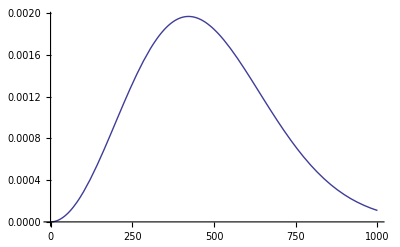

```mathematica
Plot[mb[u],{u,0,1000}]
```

```mathematica
uavg=Assuming[{m>0,r>0,t>0},Integrate[mb[u],{u,300,500}]]
```

0.37632

```mathematica
(*caculate the prob. of the electron in a 1s orbital in the hydrogen atom is within the Bohr radius of the nucleus*)
```

```mathematica
Clear[r]
```

```mathematica
f[r_]:=2 (1/a0)^(3/2)E^(-r/a0);
prob=Integrate[r^2 f[r]^2,{r,0,a0}]
```

1-5/ⅇ^2

```mathematica
N[%]
```

0.323324

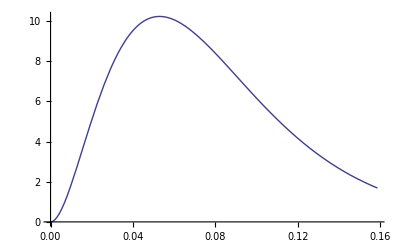

```mathematica
a0=0.0529;
Plot[r^2 f[r]^2,{r,0,3*a0}]
```

```mathematica
(*equation solving*)
```

```mathematica
Solve[x+1==0,x]
```

{{x→-1}}

```mathematica
(*solve quadratic equation*)
```

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
(*extract out*)
```

```mathematica
roots=Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
root1=roots[[1]]
```

{x→(-b-√(b^2-4 a c))/(2 a)}

```mathematica
root2=roots[[2]]
```

{x→(-b+√(b^2-4 a c))/(2 a)}

```mathematica
roots/.{a->1,b->3,c->1}
```

{{x→1/2 (-3-√5)},{x→1/2 (-3+√5)}}

```mathematica
N[%]
```

{{x→-2.61803},{x→-0.381966}}

```mathematica
Solve[a x^3+b x^2+c x+d==0,x]
```

{{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)}}

```mathematica
%/.{a->1,b->2,c->3,d->4}
```

{{x→-2/3-5/3 (2/(-70+30 √6))^(1/3)+1/3 (1/2 (-70+30 √6))^(1/3)},{x→-2/3-1/6 (1-ⅈ √3) (1/2 (-70+30 √6))^(1/3)+(5 (1+ⅈ √3))/(3 2^(2/3) (-70+30 √6)^(1/3))},{x→-2/3-1/6 (1+ⅈ √3) (1/2 (-70+30 √6))^(1/3)+(5 (1-ⅈ √3))/(3 2^(2/3) (-70+30 √6)^(1/3))}}

```mathematica
N[%]
```

{{x→-1.65063},{x→-0.174685+1.54687 ⅈ},{x→-0.174685-1.54687 ⅈ}}